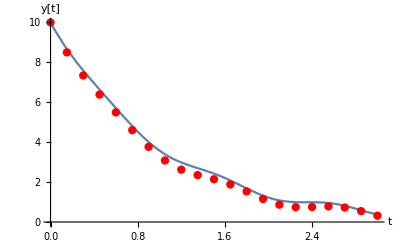

```mathematica
derivative[{t_, y_}]:= -y + Sin[6t];
tStart = 0.;
yStart = 10.;
initialPoint = {tStart, yStart};
eqnForDSolve = y'[t] == derivative[{t, y[t]}];
initialForDSolve = y[tStart] == yStart;
SolDSolve = DSolve[{eqnForDSolve, initialForDSolve}, y[t], t][[1]];
tmax = 3;
PlotDSolve = Plot[y[t]/.SolDSolve, {t, tStart, tmax}, AxesLabel->{"t", "y[t]"}];
nSteps = 20;
△t = (tmax-tStart)/nSteps;
stepEuler[{t_, y_}]:= {t+△t, y + △t*derivative[{t, y}]};
solEuler = NestList[stepEuler, initialPoint, nSteps];
PlotEuler = ListPlot[solEuler, PlotStyle->{Red, PointSize[0.015]}];
Show[PlotDSolve, PlotEuler]
```

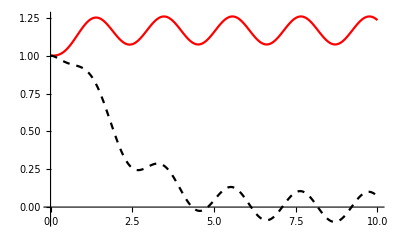

```mathematica
ClearAll["Global`*"]
eqnsDSolve = {x1'[t] == x2[t], x2'[t] == Sin[3t]-2x2[t], x1[0] == 1, x2[0] == 0};
solDSolve = DSolve[eqnsDSolve, {x1[t], x2[t]}, t][[1]];
solDS2 = DSolve[{y''[t] + 2y'[t]+ y[t] == Sin[3t], y[0] == 1, y'[0] == 0}, y[t],t];
plotDS = Plot[{x1[t]/.solDSolve, y[t]/.solDS2}, {t, 0, 10}, PlotStyle->{Red, {Dashed, Black}}]
```